```mathematica
SetOptions[Plot,BaseStyle->{FontFamily->"Helvetica",FontSize->24},Frame->True,FrameStyle->Black];SetOptions[ListPlot,BaseStyle->{FontFamily->"Helvetica",FontSize->24},Frame->True,FrameStyle->Black];M=3;
Np=4;
dim=(Np+1)^M;
Id=Table[KroneckerDelta[k1,k1p],{k1,0,Np},{k1p,0,Np}];
Sx=Table[KroneckerDelta[k1+1,k1p]*Sqrt[(k1+1)*(Np-k1)]+KroneckerDelta[k1,k1p+1]*Sqrt[(k1p+1)*(Np-k1p)],{k1,0,Np},{k1p,0,Np}];
Sy=Table[-I*KroneckerDelta[k1+1,k1p]*Sqrt[(k1+1)*(Np-k1)]+I*KroneckerDelta[k1,k1p+1]*Sqrt[(k1p+1)*(Np-k1p)],{k1,0,Np},{k1p,0,Np}];
Sz=Table[KroneckerDelta[k1,k1p]*(2*k1-Np),{k1,0,Np},{k1p,0,Np}];
Ham12=1.0*(KroneckerProduct[Sz,Id,Id]-KroneckerProduct[Id,Sz,Id]);
Ham23=1.0*(KroneckerProduct[Id,Sz,Id]-KroneckerProduct[Id,Id,Sz]);
Ham123=1.0*(-KroneckerProduct[Sx,Id,Id]-KroneckerProduct[Id,Sx,Id]-KroneckerProduct[Id,Id,Sx]-Np*KroneckerProduct[Id,Id,Id]);
```

#### Warning: This code only works if the energies happen to be integers

```mathematica
sol=Eigensystem[Ham12];
En=Round[sol[[1]]];
Enlist12=Sort[DeleteDuplicates[En]];
Enstates=sol[[2]];
entarget12=Position[Enlist12,0][[1]][[1]];
For[enelem=1,enelem≤Length[Enlist12],enelem=enelem+1,
P12[enelem]=Table[0,{ns,1,dim},{nsp,1,dim}];
];
For[n=1,n≤Length[En],n=n+1,
energy=En[[n]];
enelem=Position[Enlist12,energy][[1]][[1]];
P12[enelem]=P12[enelem]+TensorProduct[Enstates[[n]],Conjugate[Enstates[[n]]]];
];
P12num=Length[Enlist12];

sol=Eigensystem[Ham23];
En=Round[sol[[1]]];
Enlist23=Sort[DeleteDuplicates[En]];
Enstates=sol[[2]];
entarget23=Position[Enlist23,0][[1]][[1]];
For[enelem=1,enelem≤Length[Enlist23],enelem=enelem+1,
P23[enelem]=Table[0,{ns,1,dim},{nsp,1,dim}];
];
For[n=1,n≤Length[En],n=n+1,
energy=En[[n]];
enelem=Position[Enlist23,energy][[1]][[1]];
P23[enelem]=P23[enelem]+TensorProduct[Enstates[[n]],Conjugate[Enstates[[n]]]];
];
P23num=Length[Enlist23];

sol=Eigensystem[Ham123];
En=Round[sol[[1]]];
Enlist123=Sort[DeleteDuplicates[En]];
Enstates=sol[[2]];
entarget123=Position[Enlist123,0][[1]][[1]];
For[enelem=1,enelem≤Length[Enlist123],enelem=enelem+1,
P123[enelem]=Table[0,{ns,1,dim},{nsp,1,dim}];
];
For[n=1,n≤Length[En],n=n+1,
energy=En[[n]];
enelem=Position[Enlist123,energy][[1]][[1]];
P123[enelem]=P123[enelem]+TensorProduct[Enstates[[n]],Conjugate[Enstates[[n]]]];
];
P123num=Length[Enlist123];
```

```mathematica
Aflip12=KroneckerProduct[MatrixExp[I*Sx*Pi/4],MatrixExp[-I*Sx*Pi/4],Id];
Aflip23=KroneckerProduct[Id,MatrixExp[-I*Sx*Pi/4],MatrixExp[I*Sx*Pi/4]];
Aflip123=KroneckerProduct[MatrixExp[I*Sz*Pi/2],Id,Id];Total[Total[Abs[Sum[P12[n],{n,1,P12num}]-IdentityMatrix[dim]]]]
Total[Total[Abs[Sum[P23[n],{n,1,P23num}]-IdentityMatrix[dim]]]]
Total[Total[Abs[Sum[P123[n],{n,1,P123num}]-IdentityMatrix[dim]]]]
```

0.

0.

3.17206×10^-12

```mathematica
psi0=Normalize[Table[1-2*RandomReal[]+I*(1-2*RandomReal[]),{k,1,dim}]];
psi=psi0;
psic4=Normalize[ArrayReshape[Table[KroneckerDelta[k1,k2,k3]*Sqrt[Binomial[Np,k1]],{k1,0,Np},{k2,0,Np},{k3,0,Np}],{1,(Np+1)^M}][[1]]];
psighzorig=Normalize[ArrayReshape[Table[KroneckerDelta[k1,k2,k3]/Sqrt[Binomial[Np,k1]],{k1,0,Np},{k2,0,Np},{k3,0,Np}],{1,(Np+1)^M}][[1]]];
targetproj12=ArrayReshape[Table[KroneckerDelta[k1,k2]*KroneckerDelta[k1,k1p]*KroneckerDelta[k2,k2p]*KroneckerDelta[k3,k3p],{k1,0,Np},{k2,0,Np},{k3,0,Np},{k1p,0,Np},{k2p,0,Np},{k3p,0,Np}],{(Np+1)^M,(Np+1)^M}];
targetproj23=ArrayReshape[Table[KroneckerDelta[k2,k3]*KroneckerDelta[k1,k1p]*KroneckerDelta[k2,k2p]*KroneckerDelta[k3,k3p],{k1,0,Np},{k2,0,Np},{k3,0,Np},{k1p,0,Np},{k2p,0,Np},{k3p,0,Np}],{(Np+1)^M,(Np+1)^M}];
targetproj123z=ArrayReshape[Table[(KroneckerDelta[-2*k1-2*k2-2*k3+2*Np+2,2]+KroneckerDelta[-2*k1-2*k2-2*k3+2*Np+2,-2])*KroneckerDelta[k1,k1p]*KroneckerDelta[k2,k2p]*KroneckerDelta[k3,k3p],{k1,0,Np},{k2,0,Np},{k3,0,Np},{k1p,0,Np},{k2p,0,Np},{k3p,0,Np}],{(Np+1)^M,(Np+1)^M}];
Urotzx=MatrixExp[-I*Sy*Pi/4];
Urotzxall=KroneckerProduct[Urotzx,Urotzx,Urotzx];
targetproj123=ConjugateTranspose[Urotzxall].targetproj123z.Urotzxall;
```

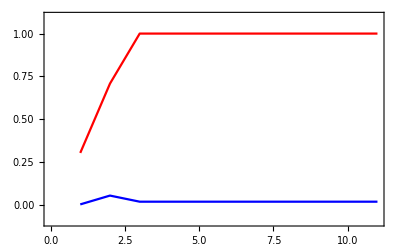

psi={0.00365364-0.0650982 ⅈ,0.0209697+0.0196574 ⅈ,0.0189933+0.0355796 ⅈ,-0.0607598-0.00210666 ⅈ,0.0115007+0.0247218 ⅈ,-0.0209697-0.0196574 ⅈ,-0.0269155+0.0215223 ⅈ,0.0487327-0.0214952 ⅈ,-0.0347625-0.0682978 ⅈ,0.0607598+0.00210666 ⅈ,0.0189933+0.0355796 ⅈ,-0.0487327+0.0214952 ⅈ,0.0461702+0.0177249 ⅈ,-0.0487327+0.0214952 ⅈ,0.0189933+0.0355796 ⅈ,0.0607598+0.00210666 ⅈ,-0.0347625-0.0682978 ⅈ,0.0487327-0.0214952 ⅈ,-0.0269155+0.0215223 ⅈ,-0.0209697-0.0196574 ⅈ,0.0115007+0.0247218 ⅈ,-0.0607598-0.00210666 ⅈ,0.0189933+0.0355796 ⅈ,0.0209697+0.0196574 ⅈ,0.00365364-0.0650982 ⅈ,-0.00730728+0.130196 ⅈ,-0.0419395-0.0393149 ⅈ,-0.0379865-0.0711593 ⅈ,0.12152+0.00421333 ⅈ,-0.0230013-0.0494437 ⅈ,0.0419395+0.0393149 ⅈ,0.0538311-0.0430445 ⅈ,-0.0974654+0.0429905 ⅈ,0.0695251+0.136596 ⅈ,-0.12152-0.00421333 ⅈ,-0.0379865-0.0711593 ⅈ,0.0974654-0.0429905 ⅈ,-0.0923403-0.0354498 ⅈ,0.0974654-0.0429905 ⅈ,-0.0379865-0.0711593 ⅈ,-0.12152-0.00421333 ⅈ,0.0695251+0.136596 ⅈ,-0.0974654+0.0429905 ⅈ,0.0538311-0.0430445 ⅈ,0.0419395+0.0393149 ⅈ,-0.0230013-0.0494437 ⅈ,0.12152+0.00421333 ⅈ,-0.0379865-0.0711593 ⅈ,-0.0419395-0.0393149 ⅈ,-0.00730728+0.130196 ⅈ,0.00894955-0.159457 ⅈ,0.0513652+0.0481507 ⅈ,0.0465238+0.0871519 ⅈ,-0.148831-0.00516025 ⅈ,0.0281707+0.0605559 ⅈ,-0.0513652-0.0481507 ⅈ,-0.0659293+0.0527186 ⅈ,0.11937-0.0526523 ⅈ,-0.0851505-0.167295 ⅈ,0.148831+0.00516025 ⅈ,0.0465238+0.0871519 ⅈ,-0.11937+0.0526523 ⅈ,0.113093+0.0434169 ⅈ,-0.11937+0.0526523 ⅈ,0.0465238+0.0871519 ⅈ,0.148831+0.00516025 ⅈ,-0.0851505-0.167295 ⅈ,0.11937-0.0526523 ⅈ,-0.0659293+0.0527186 ⅈ,-0.0513652-0.0481507 ⅈ,0.0281707+0.0605559 ⅈ,-0.148831-0.00516025 ⅈ,0.0465238+0.0871519 ⅈ,0.0513652+0.0481507 ⅈ,0.00894955-0.159457 ⅈ,-0.00730728+0.130196 ⅈ,-0.0419395-0.0393149 ⅈ,-0.0379865-0.0711593 ⅈ,0.12152+0.00421333 ⅈ,-0.0230013-0.0494437 ⅈ,0.0419395+0.0393149 ⅈ,0.0538311-0.0430445 ⅈ,-0.0974654+0.0429905 ⅈ,0.0695251+0.136596 ⅈ,-0.12152-0.00421333 ⅈ,-0.0379865-0.0711593 ⅈ,0.0974654-0.0429905 ⅈ,-0.0923403-0.0354498 ⅈ,0.0974654-0.0429905 ⅈ,-0.0379865-0.0711593 ⅈ,-0.12152-0.00421333 ⅈ,0.0695251+0.136596 ⅈ,-0.0974654+0.0429905 ⅈ,0.0538311-0.0430445 ⅈ,0.0419395+0.0393149 ⅈ,-0.0230013-0.0494437 ⅈ,0.12152+0.00421333 ⅈ,-0.0379865-0.0711593 ⅈ,-0.0419395-0.0393149 ⅈ,-0.00730728+0.130196 ⅈ,0.00365364-0.0650982 ⅈ,0.0209697+0.0196574 ⅈ,0.0189933+0.0355796 ⅈ,-0.0607598-0.00210666 ⅈ,0.0115007+0.0247218 ⅈ,-0.0209697-0.0196574 ⅈ,-0.0269155+0.0215223 ⅈ,0.0487327-0.0214952 ⅈ,-0.0347625-0.0682978 ⅈ,0.0607598+0.00210666 ⅈ,0.0189933+0.0355796 ⅈ,-0.0487327+0.0214952 ⅈ,0.0461702+0.0177249 ⅈ,-0.0487327+0.0214952 ⅈ,0.0189933+0.0355796 ⅈ,0.0607598+0.00210666 ⅈ,-0.0347625-0.0682978 ⅈ,0.0487327-0.0214952 ⅈ,-0.0269155+0.0215223 ⅈ,-0.0209697-0.0196574 ⅈ,0.0115007+0.0247218 ⅈ,-0.0607598-0.00210666 ⅈ,0.0189933+0.0355796 ⅈ,0.0209697+0.0196574 ⅈ,0.00365364-0.0650982 ⅈ}

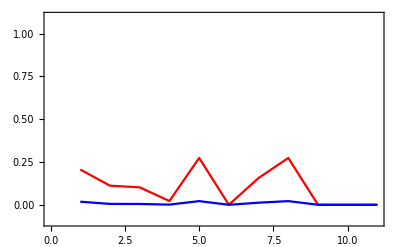

psi={0,0,0,0,0,0.00496983+0.0545106 ⅈ,-0.00546508-0.02213 ⅈ,-0.0315448-0.0180657 ⅈ,0.0568489+0.0263765 ⅈ,-0.0304688-0.0187519 ⅈ,0.0445077-0.00405785 ⅈ,-0.0180691+0.00446222 ⅈ,-0.0147506+0.0257562 ⅈ,0.0215363-0.0464169 ⅈ,-0.0153108+0.0248777 ⅈ,0.0115963+0.127191 ⅈ,-0.0127519-0.0516367 ⅈ,-0.0736045-0.0421533 ⅈ,0.132647+0.0615452 ⅈ,-0.0710938-0.0437543 ⅈ,0.254383-0.0231926 ⅈ,-0.103273+0.0255037 ⅈ,-0.0843065+0.147209 ⅈ,0.12309-0.265295 ⅈ,-0.0875086+0.142188 ⅈ,-0.00496983-0.0545106 ⅈ,0.00546508+0.02213 ⅈ,0.0315448+0.0180657 ⅈ,-0.0568489-0.0263765 ⅈ,0.0304688+0.0187519 ⅈ,0,0,0,0,0,-0.0121736-0.133523 ⅈ,0.0133867+0.0542072 ⅈ,0.0772687+0.0442517 ⅈ,-0.139251-0.064609 ⅈ,0.074633+0.0459325 ⅈ,-0.0726807+0.00662644 ⅈ,0.0295067-0.00728678 ⅈ,0.0240876-0.0420597 ⅈ,-0.0351687+0.0757985 ⅈ,0.0250025-0.040625 ⅈ,-0.0115963-0.127191 ⅈ,0.0127519+0.0516367 ⅈ,0.0736045+0.0421533 ⅈ,-0.132647-0.0615452 ⅈ,0.0710938+0.0437543 ⅈ,-0.0445077+0.00405785 ⅈ,0.0180691-0.00446222 ⅈ,0.0147506-0.0257562 ⅈ,-0.0215363+0.0464169 ⅈ,0.0153108-0.0248777 ⅈ,0.0121736+0.133523 ⅈ,-0.0133867-0.0542072 ⅈ,-0.0772687-0.0442517 ⅈ,0.139251+0.064609 ⅈ,-0.074633-0.0459325 ⅈ,0,0,0,0,0,0.0121736+0.133523 ⅈ,-0.0133867-0.0542072 ⅈ,-0.0772687-0.0442517 ⅈ,0.139251+0.064609 ⅈ,-0.074633-0.0459325 ⅈ,0.0445077-0.00405785 ⅈ,-0.0180691+0.00446222 ⅈ,-0.0147506+0.0257562 ⅈ,0.0215363-0.0464169 ⅈ,-0.0153108+0.0248777 ⅈ,-0.0115963-0.127191 ⅈ,0.0127519+0.0516367 ⅈ,0.0736045+0.0421533 ⅈ,-0.132647-0.0615452 ⅈ,0.0710938+0.0437543 ⅈ,0.0726807-0.00662644 ⅈ,-0.0295067+0.00728678 ⅈ,-0.0240876+0.0420597 ⅈ,0.0351687-0.0757985 ⅈ,-0.0250025+0.040625 ⅈ,-0.0121736-0.133523 ⅈ,0.0133867+0.0542072 ⅈ,0.0772687+0.0442517 ⅈ,-0.139251-0.064609 ⅈ,0.074633+0.0459325 ⅈ,0,0,0,0,0,-0.00496983-0.0545106 ⅈ,0.00546508+0.02213 ⅈ,0.0315448+0.0180657 ⅈ,-0.0568489-0.0263765 ⅈ,0.0304688+0.0187519 ⅈ,-0.254383+0.0231926 ⅈ,0.103273-0.0255037 ⅈ,0.0843065-0.147209 ⅈ,-0.12309+0.265295 ⅈ,0.0875086-0.142188 ⅈ,0.0115963+0.127191 ⅈ,-0.0127519-0.0516367 ⅈ,-0.0736045-0.0421533 ⅈ,0.132647+0.0615452 ⅈ,-0.0710938-0.0437543 ⅈ,-0.0445077+0.00405785 ⅈ,0.0180691-0.00446222 ⅈ,0.0147506-0.0257562 ⅈ,-0.0215363+0.0464169 ⅈ,0.0153108-0.0248777 ⅈ,0.00496983+0.0545106 ⅈ,-0.00546508-0.02213 ⅈ,-0.0315448-0.0180657 ⅈ,0.0568489+0.0263765 ⅈ,-0.0304688-0.0187519 ⅈ,0,0,0,0,0}

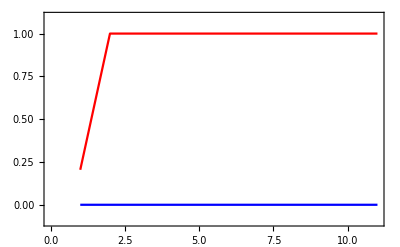

psi={0,0,0,0,0,0,-0.0120881-0.0489489 ⅈ,0,0,0,0,0,-0.0326265+0.0569696 ⅈ,0,0,0,0,0,0.2934+0.13613 ⅈ,0,0,0,0,0,-0.193558+0.314502 ⅈ,-0.0109927-0.120571 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0.170909+0.0978794 ⅈ,0,0,0,0,0,-0.0777888+0.167657 ⅈ,0,0,0,0,0,0.157251+0.0967792 ⅈ,-0.0984456+0.00897548 ⅈ,0,0,0,0,0,-0.0296097-0.1199 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0.308006+0.142907 ⅈ,0,0,0,0,0,-0.0338657+0.0550264 ⅈ,-0.0256496-0.281332 ⅈ,0,0,0,0,0,-0.0652652+0.0161175 ⅈ,0,0,0,0,0,0.170909+0.0978794 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0.0673932+0.0414768 ⅈ,-0.562663+0.0512991 ⅈ,0,0,0,0,0,-0.0282056-0.114214 ⅈ,0,0,0,0,0,0.0326265-0.0569696 ⅈ,0,0,0,0,0,0.125743+0.0583416 ⅈ,0,0,0,0,0,0}

```mathematica
nmax=10;
maxiter=100;
fidval=Conjugate[psi].targetproj123.psi;
fidlist={fidval};
fidvalc4=Abs[Conjugate[psi].psic4]^2;
fidlistc4={fidvalc4};
Eestlist={};

For[n=1,n≤nmax,n=n+1,
found=0;
For[iter=1,iter≤maxiter,iter=iter+1,
m=RandomInteger[{1,P123num}];
ptry=RandomReal[];
psi1=P123[m].psi;
prob1=Norm[psi1]^2;
If[ptry<prob1,
psi=Normalize[psi1];
found=1;
Break[];
];
];

If [m!=entarget123,
psi=Aflip123.psi;
];

If[found==0,Print["not found Ham1"]];

fidval=Conjugate[psi].targetproj123.psi;
fidlist=Append[fidlist,fidval];
fidvalc4=Abs[Conjugate[psi].psic4]^2;
fidlistc4=Append[fidlistc4,fidvalc4];

];
p1=ListPlot[{fidlist,fidlistc4},PlotStyle->{Red,Blue,Green},PlotRange->{-0.1,1.1},Joined->True];
Show[p1]

Print["psi=",Chop[psi]];


fidval=Conjugate[psi].targetproj12.psi;
fidlist={fidval};
fidvalc4=Abs[Conjugate[psi].psic4]^2;
fidlistc4={fidvalc4};
Eestlist={};

For[n=1,n≤nmax,n=n+1,
found=0;
For[iter=1,iter≤maxiter,iter=iter+1,
m=RandomInteger[{1,P12num}];
ptry=RandomReal[];
psi1=P12[m].psi;
prob1=Norm[psi1]^2;
If[ptry<prob1,
psi=Normalize[psi1];
found=1;
Break[];
];
];
(*Print["m=",m," ",psi];*)
If [m!=entarget12,
psi=Aflip12.psi;
];
(*Print[psi];*)

If[found==0,Print["not found Ham1"]];

fidval=Conjugate[psi].targetproj12.psi;
fidlist=Append[fidlist,fidval];
fidvalc4=Abs[Conjugate[psi].psic4]^2;
fidlistc4=Append[fidlistc4,fidvalc4];

];
p1=ListPlot[{fidlist,fidlistc4},PlotStyle->{Red,Blue,Green},PlotRange->{-0.1,1.1},Joined->True];
Show[p1]

Print["psi=",Chop[psi]];



fidval=Conjugate[psi].targetproj23.psi;
fidlist={fidval};
fidvalc4=Abs[Conjugate[psi].psic4]^2;
fidlistc4={fidvalc4};
Eestlist={};

For[n=1,n≤nmax,n=n+1,
found=0;
For[iter=1,iter≤maxiter,iter=iter+1,
m=RandomInteger[{1,P23num}];
ptry=RandomReal[];
psi1=P23[m].psi;
prob1=Norm[psi1]^2;
If[ptry<prob1,
psi=Normalize[psi1];
found=1;
Break[];
];
];

(*Print["m=",m," ",psi];*)

If [m!=entarget23,
psi=Aflip23.psi;
];

(*Print[psi];*)

If[found==0,Print["not found Ham1"]];

fidval=Conjugate[psi].targetproj23.psi;
fidlist=Append[fidlist,fidval];
fidvalc4=Abs[Conjugate[psi].psic4]^2;
fidlistc4=Append[fidlistc4,fidvalc4];

];
p1=ListPlot[{fidlist,fidlistc4},PlotStyle->{Red,Blue,Green},PlotRange->{-0.1,1.1},Joined->True];
Show[p1]

Print["psi=",Chop[psi]];
```

```mathematica
sol=Eigensystem[P123[entarget123]];
sol[[1]]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,2.86127×10^-15,-1.80306×10^-15,1.64087×10^-15,1.60872×10^-15,-1.51508×10^-15,-1.24398×10^-15,-1.20414×10^-15,8.88178×10^-16,8.03785×10^-16,5.27283×10^-16,2.12253×10^-16,1.87959×10^-16,-1.43088×10^-16,8.14666×10^-17,4.84041×10^-17,4.50937×10^-17,4.32316×10^-17,3.75699×10^-17,3.61861×10^-17,-3.2479×10^-17,-3.14611×10^-17,2.98585×10^-17,2.97942×10^-17,2.9191×10^-17,-2.8317×10^-17,-2.77802×10^-17,2.67×10^-17,-2.65978×10^-17,2.64933×10^-17,-2.57844×10^-17,2.48295×10^-17,2.46018×10^-17,-2.43787×10^-17,2.41324×10^-17,2.39329×10^-17,-2.37129×10^-17,2.34078×10^-17,2.24488×10^-17,2.15974×10^-17,2.1523×10^-17,2.1061×10^-17,2.08095×10^-17,-1.93745×10^-17,1.76442×10^-17,1.73862×10^-17,1.72502×10^-17,1.7212×10^-17,1.65734×10^-17,-1.64365×10^-17,-1.51518×10^-17,-1.35878×10^-17,1.27785×10^-17,1.21527×10^-17,-1.21404×10^-17,1.20703×10^-17,1.18216×10^-17,1.15409×10^-17,1.15374×10^-17,1.1443×10^-17,1.14193×10^-17,1.14169×10^-17,-1.13499×10^-17,-1.13446×10^-17,-1.10505×10^-17,1.01521×10^-17,-1.00026×10^-17,9.56827×10^-18,-9.38538×10^-18,-9.2498×10^-18,9.02672×10^-18,8.28143×10^-18,8.05289×10^-18,-7.91122×10^-18,-7.83579×10^-18,7.64602×10^-18,7.25537×10^-18,-7.10809×10^-18,7.00068×10^-18,6.83508×10^-18,6.81094×10^-18,6.52818×10^-18,6.47094×10^-18,5.8246×10^-18,-5.75837×10^-18,5.64366×10^-18,5.43877×10^-18,5.25993×10^-18,5.13897×10^-18,4.89226×10^-18,-4.40146×10^-18,-4.38227×10^-18,3.81948×10^-18,3.49134×10^-18,-3.4384×10^-18,-3.29319×10^-18,-2.88959×10^-18,-2.82627×10^-18,2.7608×10^-18,2.62799×10^-18,2.62086×10^-18,-2.39284×10^-18,-2.26305×10^-18,1.96612×10^-18,1.87636×10^-18,1.68316×10^-18,1.59258×10^-18,-1.19879×10^-18,3.53988×10^-19,-3.39634×10^-19,1.87325×10^-19}

```mathematica
psic4.P12[entarget12].psic4
```

1.

```mathematica
For[n=1,n≤6,n=n+1,
phi=sol[[2]][[n]];
fid=phi.P12[entarget12].P23[entarget23].phi;
Print[fid]
];
```

0.0508581

0.54375

0.0688641

0.114445

0.00831631

0.0575165

```mathematica
sol[[2]][[2]]
```

{0.484123,-0.228218,-0.0322749,-0.228218,-0.0645497,0.136931,-0.0322749,0.136931,-0.0322749,-0.228218,-0.0645497,0.136931,-0.0645497,0.273861,-0.0645497,0.136931,-0.0645497,-0.228218,-0.0322749,0.136931,-0.0322749,0.136931,-0.0645497,-0.228218,-0.0322749,-0.228218,0.484123}

```mathematica
psic4.P123[entarget123].psic4
```

0.609375

```mathematica
psic4
```

{1/4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(3/2))/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/4}

```mathematica
psighzorig
```

{(√(3/2))/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(3/2))/4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(3/2))/4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(3/2))/2}

```mathematica
N[Urotzxall.psic4]
```

{0.0234375,0.,-0.0956832,0.,0.273438,0.,-0.09375,0.,0.15625,0.,-0.0956832,0.,0.140625,0.,-0.0956832,0.,0.15625,0.,-0.09375,0.,0.273438,0.,-0.0956832,0.,0.0234375,0.,-0.09375,0.,0.15625,0.,-0.09375,0.,0.0765466,0.,0.15625,0.,0.0765466,0.,0.0765466,0.,0.15625,0.,0.0765466,0.,-0.09375,0.,0.15625,0.,-0.09375,0.,-0.0956832,0.,0.140625,0.,-0.0956832,0.,0.0765466,0.,0.0765466,0.,0.140625,0.,0.0382733,0.,0.140625,0.,0.0765466,0.,0.0765466,0.,-0.0956832,0.,0.140625,0.,-0.0956832,0.,0.15625,0.,-0.09375,0.,0.15625,0.,0.0765466,0.,-0.09375,0.,0.0765466,0.,0.0765466,0.,-0.09375,0.,0.0765466,0.,0.15625,0.,-0.09375,0.,0.15625,0.,0.273438,0.,-0.0956832,0.,0.0234375,0.,0.15625,0.,-0.09375,0.,-0.0956832,0.,0.140625,0.,-0.0956832,0.,-0.09375,0.,0.15625,0.,0.0234375,0.,-0.0956832,0.,0.273438}

```mathematica
N[Urotzxall.psighzorig]
```

{0.,0.,0.,0.,0.153093,0.,0.,0.,0.153093,0.,0.,0.,0.153093,0.,0.,0.,0.153093,0.,0.,0.,0.153093,0.,0.,0.,0.,0.,0.,0.,0.153093,0.,0.,0.,0.1875,0.,0.153093,0.,0.1875,0.,0.1875,0.,0.153093,0.,0.1875,0.,0.,0.,0.153093,0.,0.,0.,0.,0.,0.153093,0.,0.,0.,0.1875,0.,0.1875,0.,0.153093,0.,0.25,0.,0.153093,0.,0.1875,0.,0.1875,0.,0.,0.,0.153093,0.,0.,0.,0.153093,0.,0.,0.,0.153093,0.,0.1875,0.,0.,0.,0.1875,0.,0.1875,0.,0.,0.,0.1875,0.,0.153093,0.,0.,0.,0.153093,0.,0.153093,0.,0.,0.,0.,0.,0.153093,0.,0.,0.,0.,0.,0.153093,0.,0.,0.,0.,0.,0.153093,0.,0.,0.,0.,0.,0.153093}

```mathematica
psighzorig
```

{(√(3/2))/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(3/2))/4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(3/2))/4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(√(3/2))/2}

```mathematica
N[psic4.psighzorig]
```

0.765466